```mathematica
V0=35;R=2.1;μ=1/2;
```

```mathematica
rmax=R;dr=0.01;
rlist=Range[0,rmax,dr];
n=Length[rlist]
```

211

```mathematica
(*V0=10;R=2;a=0.5;*)
```

```mathematica
(*V[r_]:=-V0/(1+Exp[(r-R)/a]);*)
```

```mathematica
k1[En_]:=Sqrt[2 μ(En+V0)]
```

```mathematica
Clear[En]
FindRoot[Cot[k1[En] R]==-k1[En]/k2[En],{En,-34,-V0,0}]
```

```mathematica
V1=Table[If[r≤R,-V0,0],{r,Range[0,rmax,dr]}];
```

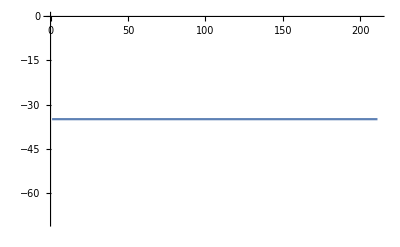

```mathematica
Vmat=DiagonalMatrix[V1];
(*Vmat=PadRight[Vmat,{n+1,n+1}];*)
ListLinePlot[V1]
```

```mathematica
ListDensityPlot[Vmat,PlotLegends->Automatic]
```

-Graphics-

```mathematica
(*calculate KE matrix*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
KE=-1/(2 μ) 1/dr^2(one[n,-1]-2 one[n,0]+one[n,1]);
```

```mathematica
H0=KE+Vmat;
{eval,evec}=Eigensystem[H0];
```

```mathematica
Manipulate[ListPlot[Transpose[{rlist,evec[[-i]]}],Joined->True,PlotRange->All],{i,1,n,1}]
```

```mathematica
eval[[-3]]
```

19.8743

```mathematica
k2[En_]:=Sqrt[-2μ En]
```

```mathematica
Hnew=H0;Hnew[[n,n]]=-1/(2 μ) 1/dr^2(-1-dr k2[eval[[-3]]]);
```

```mathematica
Hnew[[n,n]]
```

10390.4

```mathematica
{evalnew,evecnew}=Eigensystem[Hnew];
Manipulate[ListPlot[{rlist,evec⟦-i⟧}ᵀ,Joined->True,PlotRange->All],{i,1,n,1}]
```

```mathematica
evalnew[[-3]]
```

-18.2035

```mathematica
wave[En_,r_]:=Exp[-k2[En] r]
```